## Everything is a function. © Steven Wolfram

Teacher: “If Tom gave you three apples and Bill gave you two apples, 
how many apples would you have then?” 
Mary: “Seven apples, teacher.” 
Teacher: “Wrong, Mary, 3 + 2 = 5.” 
Mary: “I know that, teacher, but I have two apples already.”

### Работа с выражениями

Map[fun, expr]	fun /@ expr

Apply[fun, expr]		fun @@ expr

```mathematica
?Map
```

RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"]}], "]"}] or RowBox[{StyleBox["f", "TI"], "/@", StyleBox["expr", "TI"]}] applies StyleBox["f", "TI"] to each element on the first level in StyleBox["expr", "TI"]. 
RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] applies StyleBox["f", "TI"] to parts of StyleBox["expr", "TI"] specified by StyleBox["levelspec", "TI"].

```mathematica
Map[Head,{3,22/7,π}] (*к каждому элементу списка*)
```

{Integer,Rational,Symbol}

```mathematica
Map[h,{a,b,c}]
```

{h[a],h[b],h[c]}

```mathematica
Map[h,g[a,b,c]] (*зависит от уровня, по умол на первом*)
```

g[h[a],h[b],h[c]]

```mathematica
Reverse[{{a,b},{c,d},{e,f}}]
```

{{e,f},{c,d},{a,b}}

```mathematica
Map[Reverse,{{a,b},{c,d},{e,f}}]
```

{{b,a},{d,c},{f,e}}

```mathematica
Sort[{{7,4,1,3},{2,6,3,5}}]
```

{{2,6,3,5},{7,4,1,3}}

```mathematica
Map[Sort,{{7,4,1,3},{2,6,3,5}}]
```

{{1,3,4,7},{2,3,5,6}}

```mathematica
{Sin[{a,b,c}],Map[Sin,{a,b,c}]}
```

{{Sin[a],Sin[b],Sin[c]},{Sin[a],Sin[b],Sin[c]}}

```mathematica
vec={1.5,π,I};
```

```mathematica
f[x_]:=x^2+1;
```

```mathematica
f[vec]
```

{3.25,1+π^2,0}

```mathematica
Map[f,vec]
```

{3.25,1+π^2,0}

```mathematica
f/@vec
```

{3.25,1+π^2,0}

```mathematica
?Apply
```

RowBox[{"Apply", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"]}], "]"}] or RowBox[{StyleBox["f", "TI"], "@@", StyleBox["expr", "TI"]}] replaces the head of StyleBox["expr", "TI"] by StyleBox["f", "TI"]. 
RowBox[{"Apply", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", RowBox[{"{", "1", "}"}]}], "]"}] or RowBox[{StyleBox["f", "TI"], "@@@", StyleBox["expr", "TI"]}] replaces heads at level 1 of StyleBox["expr", "TI"] by StyleBox["f", "TI"].
RowBox[{"Apply", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] replaces heads in parts of StyleBox["expr", "TI"] specified by StyleBox["levelspec", "TI"].

```mathematica
Apply[h,g[a,b,c]] (*ко всему списку *)
```

h[a,b,c]

```mathematica
Apply[h,{a,b,c}]
```

h[a,b,c]

```mathematica
h@@{a,b,c}
```

h[a,b,c]

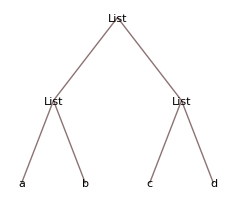

```mathematica
TreeForm[{{a,b},{c,d}}]
```

```mathematica
Map[h,{{a,b},{c,d}}]
```

{h[{a,b}],h[{c,d}]}

```mathematica
Map[h,{{a,b},{c,d}},{2}]
```

{{h[a],h[b]},{h[c],h[d]}}

```mathematica
Apply[h,{{a,b},{c,d}}] (*на уровне 0*)
```

h[{a,b},{c,d}]

```mathematica
Apply[h,{{a,b},{c,d}},{1}]
```

{h[a,b],h[c,d]}

Thread

```mathematica
?Thread
```

RowBox[{"Thread", "[", RowBox[{StyleBox["f", "TI"], "[", StyleBox["args", "TI"], "]"}], "]"}] "threads" StyleBox["f", "TI"] over any lists that appear in StyleBox["args", "TI"]. 
RowBox[{"Thread", "[", RowBox[{RowBox[{StyleBox["f", "TI"], "[", StyleBox["args", "TI"], "]"}], ",", StyleBox["h", "TI"]}], "]"}] threads StyleBox["f", "TI"] over any objects with head StyleBox["h", "TI"] that appear in StyleBox["args", "TI"]. 
RowBox[{"Thread", "[", RowBox[{RowBox[{StyleBox["f", "TI"], "[", StyleBox["args", "TI"], "]"}], ",", StyleBox["h", "TI"], ",", StyleBox["n", "TI"]}], "]"}] threads StyleBox["f", "TI"] over objects with head StyleBox["h", "TI"] that appear in the first StyleBox["n", "TI"] StyleBox["args", "TI"].

```mathematica
Thread[g[{a,b,c},{x,y,z}]]
```

{g[a,x],g[b,y],g[c,z]}

```mathematica
MapThread[g,{{a,b,c},{x,y,z}}]
```

{g[a,x],g[b,y],g[c,z]}

```mathematica
Transpose[{{a,b,c},{x,y,z}}]
Apply[g,%,{1}]
```

{{a,x},{b,y},{c,z}}

{g[a,x],g[b,y],g[c,z]}

```mathematica
Thread[{x,y,z}=={a,b,c}]
```

{x==a,y==b,z==c}

```mathematica
vars={x1,x2,x3,x4,x5};
```

```mathematica
values={1.2,2.5,5.7,8.21,6.66};
```

```mathematica
Rule[vars,values](* a rule of lists *)
```

{x1,x2,x3,x4,x5}→{1.2,2.5,5.7,8.21,6.66}

```mathematica
Thread[Rule[vars,values]] (* list of rules *)
```

{x1→1.2,x2→2.5,x3→5.7,x4→8.21,x5→6.66}



```mathematica
Graphics[Circle[{0,0},1]] (*рисуем окружность*)
```

```mathematica
radii={0.5,1.0,0.5};
centers={{-1,0},{0,0},{1,0}};
```

```mathematica
Thread[Circle[centers,radii]]
```

{Circle[{-1,0},0.5],Circle[{0,0},1.],Circle[{1,0},0.5]}

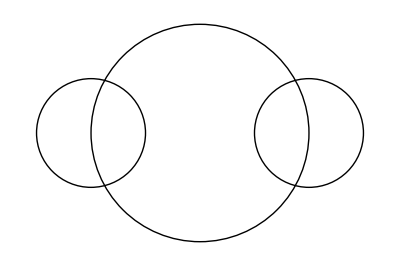

```mathematica
Graphics[%]
```

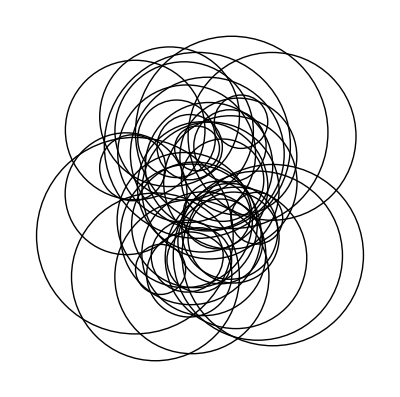

```mathematica
radii=RandomReal[{.25,1.25},{40}];
centers=RandomReal[{-1,1},{40,2}];
Graphics[Thread[Circle[centers,radii]]]
```

```mathematica
Graphics[MapThread[Circle,{centers,radii}]]
```

-Graphics-

Inner
Outer

```mathematica
?Inner
```

RowBox[{"Inner", "[", RowBox[{StyleBox["f", "TI"], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["g", "TI"]}], "]"}] is a generalization of Dot in which StyleBox["f", "TI"] plays the role of multiplication and StyleBox["g", "TI"] of addition.

```mathematica
?Outer
```

RowBox[{"Outer", "[", RowBox[{StyleBox["f", "TI"], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] gives the generalized outer product of the SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]], forming all possible combinations of the lowest-level elements in each of them, and feeding them as arguments to StyleBox["f", "TI"]. 
RowBox[{"Outer", "[", RowBox[{StyleBox["f", "TI"], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"], ",", StyleBox["n", "TI"]}], "]"}] treats as separate elements only sublists at level StyleBox["n", "TI"] in the SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Outer", "[", RowBox[{StyleBox["f", "TI"], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] treats as separate elements only sublists at level SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]] in the corresponding SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]].

```mathematica
Outer[ff,{x,y},{2,3,4}]
```

{{ff[x,2],ff[x,3],ff[x,4]},{ff[y,2],ff[y,3],ff[y,4]}}

```mathematica
Outer[Times,{u1,u2,u3},{v1,v2,v3,v4}]//MatrixForm
```

(u1 v1 | u1 v2 | u1 v3 | u1 v4
u2 v1 | u2 v2 | u2 v3 | u2 v4
u3 v1 | u3 v2 | u3 v3 | u3 v4)

```mathematica
Inner[ff,{x,y,z},{d,e,f},g]
```

g[ff[x,d],ff[y,e],ff[z,f]]

```mathematica
Inner[Equal,{x,y,z},{a,b,c},List]
```

{x==a,y==b,z==c}

```mathematica
Inner[Times,{x1,y1,z1},{x2,y2,z2},Plus]
```

x1 x2+y1 y2+z1 z2

```mathematica
Dot[{x1,y1,z1},{x2,y2,z2}]
```

x1 x2+y1 y2+z1 z2

Select and Pick

```mathematica
Select[{1,2,3,4,5,6,7,8,9},EvenQ]
```

{2,4,6,8}

```mathematica
Select[Table[2^n-1,{n,1,100}],PrimeQ]
```

{3,7,31,127,8191,131071,524287,2147483647,2305843009213693951,618970019642690137449562111}

```mathematica
data={24.39001,29.669,9.321,10.8856,23.4736,22.1488,14.7434,22.1619,21.1039,34.8177,27.1331,25.8705,39.7676,24.7762};
```

```mathematica
inRange[x_]:=20≤x≤30
```

```mathematica
inRange/@{19,25,31}
```

{False,True,False}

```mathematica
Select[data,inRange]
```

{24.39,29.669,23.4736,22.1488,22.1619,21.1039,27.1331,25.8705,24.7762}

```mathematica
Pick[{a,b,c,d,e},{True,False,True,False,True}]
```

{a,c,e}

```mathematica
Pick[{a,b,c,d,e},{1,0,1,0,1},0]
```

{b,d}

### Итерации

Nest
NestList
NestWhile
Fold

```mathematica
NestList[g,a,4](*применяем g последовательно 4 раза*)
```

{a,g[a],g[g[a]],g[g[g[a]]],g[g[g[g[a]]]]}

```mathematica
Nest[g,a,4] (**)
```

g[g[g[g[a]]]]

```mathematica
NestList[Cos,0.85,6]
```

{0.85,0.659983,0.790003,0.703843,0.76236,0.723208,0.749687}

```mathematica
{0.85,Cos[0.85],Cos[Cos[0.85]],Cos[Cos[Cos[0.85]]]}
```

{0.85,0.659983,0.790003,0.703843}

```mathematica
ff[x_]:=1/(1+x)
```

```mathematica
Nest[ff,x,5]
```

1/(1+1/(1+1/(1+1/(1+1/(1+x)))))

```mathematica
vertices={{0,0},{1,0},{1/2,√3/2}};
tri10=Triangle[vertices];
```

```mathematica
tri8=Polygon[vertices];
```

```mathematica
Graphics[{LightBlue,EdgeForm[Gray],tri8}]
```

-Graphics-

```mathematica
rotation[gr_]:=Rotate[gr,π/13]
```

```mathematica
Graphics[{LightBlue,Opacity[.5],EdgeForm[Gray],NestList[rotation,tri8,10]
}]
```

-Graphics-

```mathematica
vecs=1/2 vertices
```

{{0,0},{1/2,0},{1/4,(√3)/4}}

```mathematica
translation[gr_]:=Translate[gr,vecs]
```

```mathematica
Graphics[{Opacity[0],EdgeForm[Gray],NestList[translation,tri8,2],EdgeForm[{Red,Thick}],tri8}]
```

-Graphics-

```mathematica
addOne[n_]:=n+1
```

```mathematica
NestWhile[addOne,2^10,CompositeQ]
```

1024

```mathematica
PrimeQ[%]
```

False

```mathematica
FoldList[ff,x,{a,b,c}]
```

{x,ff[x,a],ff[ff[x,a],b],ff[ff[ff[x,a],b],c]}

```mathematica
Fold[ff,x,{a,b,c}]
```

ff[ff[ff[x,a],b],c]

```mathematica
FoldList[Plus,0,{a,b,c,d,e}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

```mathematica
FoldList[Plus,0,{1,2,3,4,5}]
```

{0,1,3,6,10,15}

```mathematica
Accumulate[{1,2,3,4,5}]
```

{1,3,6,10,15}

### Явное задание функций

Паттерн/pattern x_    
Одиночный паттерн (“пустышка”, “Blank”) - любое число,символ, выражение, чтоугодно

```mathematica
Clear[g]
```

```mathematica
g[x_]=x^2 Exp[-x^2];
```

```mathematica
g[x]
```

ⅇ^(-x^2) x^2

```mathematica
g[y] (* замена x->y*)
```

ⅇ^(-y^2) y^2

```mathematica
g[2]
```

4/ⅇ^4

```mathematica
g[2.]
```

0.0732626

```mathematica
g["smth"]
```

smth^2 ⅇ^(-smth^2)

```mathematica
g["smth"]//FullForm
```

Times[Power["smth",2],Power[E,Times[-1,Power["smth",2]]]]

```mathematica
g[g[z]]
```

ⅇ^(-2 z^2-ⅇ^(-2 z^2) z^4) z^4

```mathematica
g[x_,y_]= x^(2+y) Exp[-x^2]; (*несколько аргументов - разные правила для разного числа аргументов*)
```

```mathematica
{g[x,y],g[x,0],g[x,2],g[x,-4],g[2,2],g[x,"smth"]}
```

{ⅇ^(-x^2) x^(2+y),ⅇ^(-x^2) x^2,ⅇ^(-x^2) x^4,(ⅇ^(-x^2))/x^2,16/ⅇ^4,ⅇ^(-x^2) x^(2+smth)}

```mathematica
g[z] (*имя функции тоже самое!*)
```

ⅇ^(-z^2) z^2

```mathematica
?g
```

Global`g

g[x_]=ⅇ^(-x^2) x^2
 
g[x_,y_]=ⅇ^(-x^2) x^(2+y)

```mathematica
(*Разные правила для разного числа аргументов*)
```

```mathematica
g[x,y,z]
```

g[x,y,z]

### Чистые функции / Pure functions

Function[var,body]  
Function[var,body][arg] замена var -> arg в теле функции

#### Чистые функции с именами

```mathematica
h = Function[x,a x^2 + b x + c]
```

Function[x,a x^2+b x+c]

```mathematica
h[Sin[ϕ]^2]
```

c+b Sin[ϕ]^2+a Sin[ϕ]^4

```mathematica
h[h[y]]
```

c+b (c+b y+a y^2)+a (c+b y+a y^2)^2

h- символ, представляющий чистую функцию

```mathematica
?h
```

Global`h

h=Function[x,a x^2+b x+c]

```mathematica
x="something";
gg=Function[x,x^2]; (*разные х!!!*)
```

```mathematica
gg[y]
```

y^2

```mathematica
h[a]
```

a^3+a b+c

```mathematica
a=2;
h[z]
h[a]
```

c+b z+2 z^2

8+2 b+c

```mathematica
Clear[a]
```

```mathematica
Clear[f1,f2,g,x,y,z];
f1[x_]:=Expand[x];
f2[y_]=Expand[y]; (*вычиcляется сразу*)
g=Function[x,Expand[x]]; (* не вычисляется только для конкретного аргумента*)
```

```mathematica
f1[(y+z)^2]
```

y^2+2 y z+z^2

```mathematica
f2[(y+z)^2]
```

(y+z)^2

```mathematica
g[(y+z)^2]
```

y^2+2 y z+z^2

Чистая функция - определяет поведение функции, а не аргументов.

```mathematica
D[h[y],y] (*явное задание аргумента*)
```

b+2 a y

```mathematica
h' (*не задавая аргумент*)
```

Function[x,b+2 a x]

```mathematica
{h'[stuff],h'[2/3]} (*вычисление для любого параметра*)
```

{b+2 a stuff,(4 a)/3+b}

#### Чистые функции нескольких переменных / Pure functions of several variables

```mathematica
s = Function[{x,y,z},x y^-3 Sin[z]]
```

Function[{x,y,z},(x Sin[z])/y^3]

```mathematica
Clear[x];
s[x,1/y,4]
```

x y^3 Sin[4]

```mathematica
s[x,x,x]
```

Sin[x]/x^2

```mathematica
s[1] (*не хватает аргументов*)
```

Function::fpct: Too many parameters in {x, y, z} to be filled from Function[{x, y, z}, x\ Sin[z]/y^3][1].

Function[{x,y,z},(x Sin[z])/y^3][1]

```mathematica
x="stuff"; y="more stuff";
h=Function[{x,y},x+y]
```

Function[{x,y},x+y]

```mathematica
h[x,y]
```

more stuff+stuff

```mathematica
Clear[a,b];
h[a,b]
```

a+b

```mathematica
Clear[x,y,z];
Function[{x,y,z},x y^2 z^3][z,x,y]
```

x^2 y^3 z

#### Функции без имени/ Анонимные функции/ Anonymous functions

```mathematica
Clear[a,b,c]
```

```mathematica
Function[x,a x^2 + b x + c]
```

Function[x,a x^2+b x+c]

```mathematica
Function[x,a x^2 + b x + c][q]
```

c+b q+a q^2

```mathematica
Function[x,a x^2 + b x + c][Tanh[y]]
```

c+b Tanh[y]+a Tanh[y]^2

```mathematica
Function[x,a x^2 + b x + c]@Tanh[y]
```

c+b Tanh[y]+a Tanh[y]^2

#### Скелет функции/ Skeletal notation

var ->#, #1, #2 без имен!!!!!!!!!!!

```mathematica
Clear[a,b,c,x]
```

```mathematica
(a #^2 + b# + c & )[x]
```

c+b x+a x^2

```mathematica
h=a #^2 + b# + c &  (*& - функция завершена*)
```

a #1^2+b #1+c&

```mathematica
h[stuff]
```

c+b stuff+a stuff^2

```mathematica
g = (#1 + 2#2) Exp[-#3^2]&;
```

```mathematica
g[x,y,z]
```

ⅇ^(-z^2) (x+2 y)

```mathematica
Clear[f1,f2];
f1=Tan; (*встроенная чистая функция*)
f2=f1'
```

Sec[#1]^2&

```mathematica
{f1[30 Degree],f2[30Degree]}
```

{1/(√3),4/3}

Замена головы
f@@expr заменяет заголовок в expr на  f;
expr={a,b,⋯},  f@@expr= f[a,b,⋯].

```mathematica
g
```

(#1+2 #2) Exp[-#3^2]&

```mathematica
args = {x,y,z};
g@@args
```

ⅇ^(-z^2) (x+2 y)

```mathematica
FullForm[args]
```

List[x,y,z]

```mathematica
g@@{x,y,z,"more stuff"}
```

ⅇ^(-z^2) (x+2 y)

```mathematica
g@@{x,y} (*слишком много аргументов*)
```

Function::slotn: Slot number 3 in (#1 + 2\ #2)\ Exp[-#3^2] & cannot be filled from ((#1 + 2\ #2)\ Exp[-#3^2] &)[x, y].

ⅇ^(-#3^2) (x+2 y)

### Пример: работа со “скелетными” функциями

Пусть нас интересует коэффициент при  x^3 в разложении (a + b x)^13

```mathematica
Expand[(a+b x)^13]//Coefficient[#,x,3]&
```

286 a^10 b^3

В общем виде, коэффициент при  x^n в разложении (a + b x)^m для произвольных n,m.

```mathematica
Clear[f];
f[n_,m_]:= Expand[(a+b x)^m]//Coefficient[#,x,n]&
```

```mathematica
f[3,13]
```

286 a^10 b^3

```mathematica
?f
```

Global`f

f[n_,m_]:=(Coefficient[#1,x,n]&)[Expand[(a+b x)^m]]

Фильтр сигнала

```mathematica
signal=Flatten@Import[FileNameJoin[{NotebookDirectory[],"spikedata.csv"}]];
```

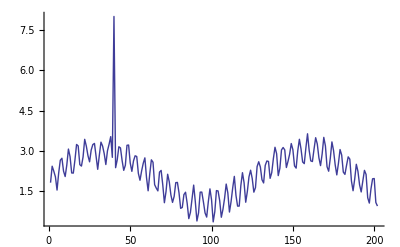

```mathematica
ListLinePlot[signal,PlotRange->All]
```

```mathematica
filtered=Select[signal,#<4&];
```

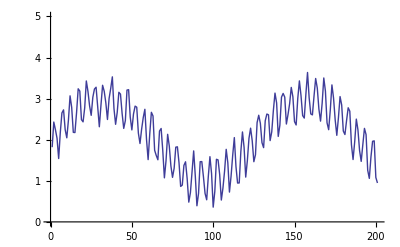

```mathematica
ListLinePlot[filtered,PlotRange->{0,5}]
```

Метод Ньютона

NestWhile[f, init, test]

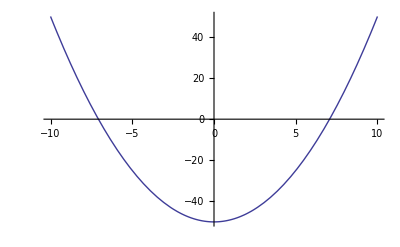

```mathematica
Plot[x^2-50,{x,-10,10}]
```

```mathematica
findRootNest[fun_,init_]:=NestWhile[#-fun[#]/fun'[#]&,N[init],Abs[fun[#]]>10^-3&]
```

```mathematica
findRootNest[#^2-50&,500]
```

7.07108

```mathematica
findRootNestList[fun_,init_]:=NestWhileList[#-fun[#]/fun'[#]&,N[init],Abs[fun[#]]>10^-3&]
```

```mathematica
findRootNestList[#^2-50&,500]
findRootNestList[#^2-50&,50]
findRootNestList[#^2-50&,5]
```

{500.,250.05,125.125,62.7623,31.7795,16.6764,9.83733,7.46,7.08121,7.07108}

{50.,25.5,13.7304,8.68597,7.22119,7.07263,7.07107}

{5.,7.5,7.08333,7.07108}

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"wi2007.txt"}],"TSV"];
```

```mathematica
Length[data]
```

1817

```mathematica
Dimensions[data]
```

{1817,2}

```mathematica
Take[data,12]
```

{{#IDA,IDB},{AC3.3,F29G6.3},{AC3.3,R05F9.10},{AC3.3,Y69H2.3},{AC3.7,Y40B10A.2},{B0001.4,F19B6.1},{B0001.7,B0281.5},{B0001.7,F37H8.1},{B0024.10,C06A1.1},{B0024.12,C06E2.1},{B0024.14,B0228.1},{B0024.14,C05G6.1}}

```mathematica
ToEdges[lis:{{_,_}..}]:=Apply[DirectedEdge,lis,{1}]
```

```mathematica
ToEdges[lis:{_,_}]:=Apply[DirectedEdge,lis]
```

```mathematica
ToEdges[Take[data,12]]
```

{#IDA->IDB,AC3.3->F29G6.3,AC3.3->R05F9.10,AC3.3->Y69H2.3,AC3.7->Y40B10A.2,B0001.4->F19B6.1,B0001.7->B0281.5,B0001.7->F37H8.1,B0024.10->C06A1.1,B0024.12->C06E2.1,B0024.14->B0228.1,B0024.14->C05G6.1}

```mathematica
edges=ToEdges[Rest[data]]; (*все кроме первого*)
```

```mathematica
gr=Graph[edges,GraphStyle->"BasicBlue"]
```

Graph[edges,GraphStyle→BasicBlue]

```mathematica
VertexDegree[gr,"R05F9.10"]
```

VertexDegree::graph: A graph object is expected at position 1 in VertexDegree[gr, "R05F9.10"].

VertexDegree[gr,R05F9.10]

```mathematica
(*ищем белки, взаимодействующие по крайней мере еще с 12 другими белками*)
```

```mathematica
VertexDegree[gr];
```

VertexDegree::graph: A graph object is expected at position 1 in VertexDegree[gr].

```mathematica
Tally@VertexDegree[gr]
```

{{3,107},{5,40},{86,1},{47,1},{1,933},{49,1},{2,246},{6,21},{8,6},{21,2},{4,64},{10,6},{7,19},{31,3},{45,1},{24,2},{14,1},{44,1},{12,11},{11,2},{28,1},{15,2},{13,2},{17,2},{9,10},{18,2},{19,3},{30,1},{16,3},{39,1},{23,1}}

```mathematica
SortBy[Tally@VertexDegree[gr],First]
```

{{1,933},{2,246},{3,107},{4,64},{5,40},{6,21},{7,19},{8,6},{9,10},{10,6},{11,2},{12,11},{13,2},{14,1},{15,2},{16,3},{17,2},{18,2},{19,3},{21,2},{23,1},{24,2},{28,1},{30,1},{31,3},{39,1},{44,1},{45,1},{47,1},{49,1},{86,1}}

```mathematica
Select[VertexList[gr],(VertexDegree[gr,#]>12&)]
```

{R05F9.10,Y69H2.3,Y40B10A.2,DH11.4,K09B11.9,R02F2.5,ZK1053.5,W05H7.4,C18G1.2,T11B7.1,F52E1.7,F46A9.5,Y54E2A.3,ZK858.4,C50F4.1,K12C11.2,C06G1.5,Y65B4BR.4,F32B4.4,ZK849.2,C36C9.1,ZK1055.7,C06A5.9,W09C2.1,F44G3.9,ZK121.2,M04G12.1,T21G5.5,W10C8.2,F01G10.2,Y55F3C.6}

```mathematica
proteins=Pick[VertexList[gr],Thread[VertexDegree[gr]>12]]
```

{R05F9.10,Y69H2.3,Y40B10A.2,DH11.4,K09B11.9,R02F2.5,ZK1053.5,W05H7.4,C18G1.2,T11B7.1,F52E1.7,F46A9.5,Y54E2A.3,ZK858.4,C50F4.1,K12C11.2,C06G1.5,Y65B4BR.4,F32B4.4,ZK849.2,C36C9.1,ZK1055.7,C06A5.9,W09C2.1,F44G3.9,ZK121.2,M04G12.1,T21G5.5,W10C8.2,F01G10.2,Y55F3C.6}

```mathematica
edges=Cases[EdgeList[gr],(p1_->p2_)/;MemberQ[proteins,p1]&&MemberQ[proteins,p2],Infinity];
```

```mathematica
edges;
```

```mathematica
{Length[edges],Take[edges,-1]}
```

{53,{ZK858.4->ZK858.4}}

```mathematica
gr1=DeleteCases[edges,x_->x_];
{Length[gr1],Take[gr1,-1]}
```

{41,{W05H7.4->ZK121.2}}

```mathematica
Graph[gr1,VertexStyle->Red,VertexSize->Large,GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]
```

-Graphics-

1. Создать функцию для нахождения корней уравнения методом Ньютона, используя критерий |x_i-x_(i+1)|<ϵ

2. Создать функцию для нахождения корней уравнения методом бисекций:
f(x)
f(a)>0; f(b)<0; 
f((a+b)/2) >0 => корень между (a+b)/2 и b
f((a+b)/2) <0 => корень между a и (a+b)/2

bisect[f,{a,b,ϵ}]
f(a)f(b)<0

3. Используя NestWhileList, создать сиракузскую последовательность 

 Берём любое натуральное число n. Если оно чётное, то делим его на 2, а если нечётное, то умножаем на 3 и прибавляем 1 (получаем 3n + 1). Над полученным числом выполняем те же самые действия, и так далее.
 
4. Определение площади круга методом Монте-Карло.